# Business Management 490

## Homework

```mathematica
Clear["`*"]
```

## Problem Set 1

### 2.)

```mathematica
a = Log[1500.]
b = .8*Log[2000]+.2*Log[100]
```

7.31322

7.00176

```mathematica
c = .25*Log[1500]+ .75*Log[100]
d = .2*Log[2000]+.8*Log[100]
```

5.28218

5.20432

### 3.)

```mathematica
Manipulate[
{{p1*Log[high1]+(1-p1)*Log[low1],p2*Log[high2]+(1-p2)*Log[low2]},{p1*high1+(1-p1)*low1,p2*high2+(1-p2)*low2}},{{p1,0.25},0,1,0.05},{{high1,130},10,200,1},{{low1,10},1,200,1},{{p2,0.2},0,1,.05},{{high2,180},10,200,1},{{low2,10},1,200,1}

]
```

Scenario A: get $100
Scenario B: 70% chance at $125 or else a 30% chance at $50

Scenario C: 25% chance to get $130 with 75% chance to get $10
Scenario D: 20% chance to get 180 with 80% chance to get $10

```mathematica
responses = ({{.08PERSON, a, b, c, d}, {Shannen, 1, 0, 1, 0}, {Chad, 1, 0, 0, 1}, {Anais, 1, 0, 0, 1}, {Mom, 1, 0, 1, 0}, {Dad, 0, 1, 0, 1}, {Dane, 0, 1, 0, 1}, {Tiffany, 0, 1, 0, 1}, {Taylor, 0, 1, 0, 1}, {Tyler, 1, 0, 0, 1}, {Cindy, 1, 0, 0, 1}})
```

(.08PERSON | a | b | c | d
Shannen | 1 | 0 | 1 | 0
Chad | 1 | 0 | 0 | 1
Anais | 1 | 0 | 0 | 1
Mom | 1 | 0 | 1 | 0
Dad | 0 | 1 | 0 | 1
Dane | 0 | 1 | 0 | 1
Tiffany | 0 | 1 | 0 | 1
Taylor | 0 | 1 | 0 | 1
Tyler | 1 | 0 | 0 | 1
Cindy | 1 | 0 | 0 | 1)

```mathematica
probabilities =Transpose[{{2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,5,4,3,2,1}/36.}];
```

### 4.)

There are 90 balls in a jar:
	30 Blue
	60 either red or yellow, but you don’t nkow how many of each.

Gamble 1: 
	1.) 100 if blue, 0- else
	2.) 100 if yellow, 0 else
	
Gamble 2: 
	1.) 100 if blue or red
	2.) 100 if red or yellow

```mathematica
responses4 = ({{.08PERSON, a, b, c, d}, {Shannen, 1, 0, 1, 0}, {Chad, 1, 0, 0, 1}, {Anais, 1, 0, 1, 0}, {Mom, 0, 1, 0, 1}, {Dad, 1, 0, 0, 1}, {Dane, 0, 1, 0, 1}, {Tiffany, 1, 0, 0, 1}, {Taylor, 1, 0, 0, 1}, {Tyler, 0, 1, 0, 1}, {Cindy, 0, 1, 0, 1}})
```

(.08PERSON | a | b | c | d
Shannen | 1 | 0 | 1 | 0
Chad | 1 | 0 | 0 | 1
Anais | 1 | 0 | 1 | 0
Mom | 0 | 1 | 0 | 1
Dad | 1 | 0 | 0 | 1
Dane | 0 | 1 | 0 | 1
Tiffany | 1 | 0 | 0 | 1
Taylor | 1 | 0 | 0 | 1
Tyler | 0 | 1 | 0 | 1
Cindy | 0 | 1 | 0 | 1)

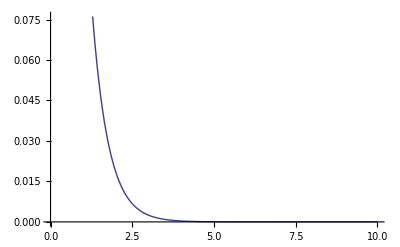

```mathematica
Plot[Exp[-2*x],{x,0,10}]
```

```mathematica
(-D[Exp[-2*w],{w,2}])/D[Exp[-2*w],w]
```

2

```mathematica
(-D[1/0.5*x^0.5,{x,2}])/D[1/0.5*x^0.5,x]
```

0.5/x^1.

### Negative Exponential Utility Function

#### Plot

#### Absolute Risk Aversion

#### Relative Risk Aversion

### Power Utility Function

#### Plot

#### Absolute Risk Aversion

#### Relative Risk Aversion

```mathematica
responses
responses4
```

(.08PERSON | a | b | c | d
Shannen | 1 | 0 | 1 | 0
Chad | 1 | 0 | 0 | 1
Anais | 1 | 0 | 0 | 1
Mom | 1 | 0 | 1 | 0
Dad | 0 | 1 | 0 | 1
Dane | 0 | 1 | 0 | 1
Tiffany | 0 | 1 | 0 | 1
Taylor | 0 | 1 | 0 | 1
Tyler | 1 | 0 | 0 | 1
Cindy | 1 | 0 | 0 | 1)

(.08PERSON | a | b | c | d
Shannen | 1 | 0 | 1 | 0
Chad | 1 | 0 | 0 | 1
Anais | 1 | 0 | 1 | 0
Mom | 0 | 1 | 0 | 1
Dad | 1 | 0 | 0 | 1
Dane | 0 | 1 | 0 | 1
Tiffany | 1 | 0 | 0 | 1
Taylor | 1 | 0 | 0 | 1
Tyler | 0 | 1 | 0 | 1
Cindy | 0 | 1 | 0 | 1)

## Problem Set 2

### 3.) Suppose  = (1,2,3) is a vector. What is the output if you type (a) ˆ2 and (b) .^2 in the MATLAB. Explain the difference why do you get these outputs.

>> x = [1, 2, 3]
x^2
x = 1 2 3
?? ? Error using ==> mpower Matrix must be square.
  >> x.^2 ans = 1 4 9

We get an error in the first output becuase Matlab trets everything like a matrix. If you try to just square something it will only work if that something can be squared in accordance with the rules of matrix algebra, in other words the matrix must be square. The dot notation, on the other hand, tells Matlab to apply the function or procedure on each element in the matrix so you get the expected (1,2,3).^2 = (1,4,9).

### 4. ) Use rand function to generate a 8 × 8 matrix. Find the maximum values (a) in each column, (b) in each row, (c) overall. Also (d) find the row and column indices of all elements that are larger than 0.25.

>> m = rand(8,8)
m =
    0.8909    0.8143    0.3517    0.3804    0.5688    0.1656    0.2290    0.1067
    0.9593    0.2435    0.8308    0.5678    0.4694    0.6020    0.9133    0.9619
    0.5472    0.9293    0.5853    0.0759    0.0119    0.2630    0.1524    0.0046
    0.1386    0.3500    0.5497    0.0540    0.3371    0.6541    0.8258    0.7749
    0.1493    0.1966    0.9172    0.5308    0.1622    0.6892    0.5383    0.8173
    0.2575    0.2511    0.2858    0.7792    0.7943    0.7482    0.9961    0.8687
    0.8407    0.6160    0.7572    0.9340    0.3112    0.4505    0.0782    0.0844
    0.2543    0.4733    0.7537    0.1299    0.5285    0.0838    0.4427    0.3998
>> columnMax = transpose(max(m,[],1))
rowMax = max(m,[],2)
totalMax = max(rowMax)
columnMax =
    0.9593
    0.9293
    0.9172
    0.9340
    0.7943
    0.7482
    0.9961
    0.9619
rowMax =
    0.8909
    0.9619
    0.9293
    0.8258
    0.9172
    0.9961
    0.9340
    0.7537
totalMax =
    0.9961
>> [i,j] = ind2sub(size(m),find(m>0.25));
x = transpose([i,j]);
transpose(x)
ans =
     1     1
     2     1
     3     1
     6     1
     7     1
     8     1
     1     2
     3     2
     4     2
     6     2
     7     2
     8     2
     1     3
     2     3
     3     3
     4     3
     5     3
     6     3
     7     3
     8     3
     1     4
     2     4
     5     4
     6     4
     7     4
     1     5
     2     5
     4     5
     6     5
     7     5
     8     5
     2     6
     3     6
     4     6
     5     6
     6     6
     7     6
     2     7
     4     7
     5     7
     6     7
     8     7
     2     8
     4     8
     5     8
     6     8
     8     8
>>

## Equations

### Separation Theorem Proof

α w_1^*+ (1-α)w_2^* = α (λ_1^*Σ^-1 μ+ δ_1^*Σ^-1 e) + (1-α)(λ_2^*Σ^-1 μ+ δ_2^*Σ^-1 e)

= (α λ_1^* + (1-α)λ_2^*)Σ^-1 μ + (α δ_1^* + (1-α)δ_2^*)Σ^-1 e

λ_3^*Σ^-1 μ + δ_3^*Σ^-1 e = w_3^*

### GMV covariance Theorem Proof

α r_p+ (1-α)r_gvm

α^2 σ_p^2+ (1-α)^2(σ^2)_gmv+2α(1-α)Cov(r_p,r_gmv)

2α (σ^2)_p - 2(1-α)(σ^2)_gmv +2(1-2α)Cov(r_p,r_gmv)=0

-2(σ^2)_gmv + 2 Cov(r_p,r_gmv) = 0 → (σ^2)_gmv = Cov(r_p,r_gmv)

### Zero Covariance/ Zero Beta Theorem Proof

Cov(r_p,r_zc) = w_zc' Σ w_p

=  w_zc' Σ(λ_p^*Σ^-1 μ+ δ_p^*Σ^-1 e)

= w_zc'(λ_p^*Σ Σ^-1 μ+ δ_p^*Σ Σ^-1 e)

=  w_zc'(λ_p^*μ+ δ_p^*e)

=   λ_p^*w_zc'μ+ δ_p^*w_zc'e → w_zc'e  = 1 by definition, w_zc'μ = μ_zc

= λ_p^*w_zc'μ+ δ_p^* = 0

μ_zc= (-(δ^*)_p)/((λ^*)_P)